```mathematica
v = {{65, 3896}, {196, 34617},
{327, 95900},
{458, 187745},
{589, 310152},
{720, 463121},
{851, 646652}}
```

{{65,3896},{196,34617},{327,95900},{458,187745},{589,310152},{720,463121},{851,646652}}

```mathematica
fit = Fit[v, {1, x, x^2}, x]
```

-2.92052+2.10419 x+0.890449 x^2

```mathematica
fit /. x -> 26501365 // DecimalForm
```

625382480005896.

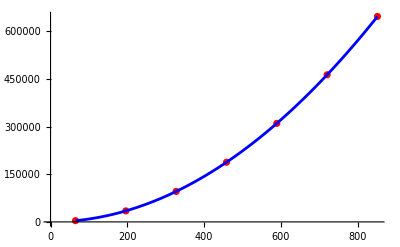

```mathematica
Show[ListPlot[v,PlotStyle->Red],Plot[fit,{x, Min[v[[All, 1]]], Max[v[[All, 1]]]},PlotStyle->Blue]  ]
```